```mathematica
D[Coth[x],x]
```

-Csch[x]^2

```mathematica
Integrate[Coth[x],x]
```

Log[Sinh[x]]

```mathematica
γCG[τ_,η_,Ω0_,β_]:=(2η)/τ NIntegrate[x Exp[-x]Coth[β x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
```

```mathematica
γCG[1,2,3,40]
```

1.5905

```mathematica
γCG[0.501939,1,1,4000]
```

0.474308

```mathematica
γCGintegTempzero[τ_,η_,Ω0_]:=(2η)/τ NIntegrate[x Exp[-x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
γCGintegTempzero[1,2,3]
```

1.59005

```mathematica
γCGintegTempzero[0.501939,1,1]
```

0.474308

```mathematica
γCGTempZero[τ_,η_,Ω0_]:=η/τ Exp[-Ω0]((1-Ω0-I Ω0 τ)ExpIntegralEi[Ω0+I Ω0 τ]+(1-Ω0+I Ω0 τ)ExpIntegralEi[Ω0-I Ω0 τ]-2(Ω0+1)ExpIntegralEi[Ω0])+(2η)/τ(1-Cos[Ω0 τ])
(*γCGTempZero[τ_,η_,Ω0_]:=η/τ Exp[-Ω0]((1+Ω0-I Ω0 τ)ExpIntegralEi[Ω0+I Ω0 τ]+(1+Ω0+I Ω0 τ)ExpIntegralEi[Ω0-I Ω0 τ]-2(Ω0+1)ExpIntegralEi[Ω0])-(2η)/τ(1-Cos[Ω0 τ])*)
```

```mathematica
γIntegral0Temp[τ_,η_,Ω0_]:=(4η)/τ NIntegrate[x Exp[-x](Sin[(Ω0-x)τ/2]/(Ω0-x))^2,{x,0,Infinity}]
γIntegral0Temp[0.501939,1,1]
γCGTempZero[0.501939,1,1]
```

0.474308

-4.09857+0. ⅈ

```mathematica
N[γCGTempZero[0.501939,1,1]]
```

0.438713+0. ⅈ

```mathematica
b=0.01;
Ω0=1;
τ=1;
NIntegrate[x Exp[-x]Coth[b x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
NIntegrate[x Exp[-x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,Infinity}]
```

46.6742

0.418714

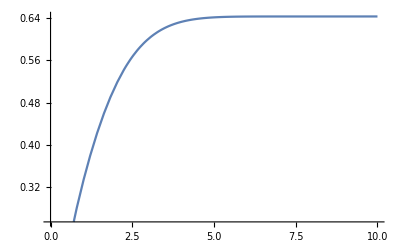

```mathematica
b=1;
Ω0=1;
τ=1;
Plot[NIntegrate[x Exp[-x]Coth[b x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,t}],{t,0,10}]
```

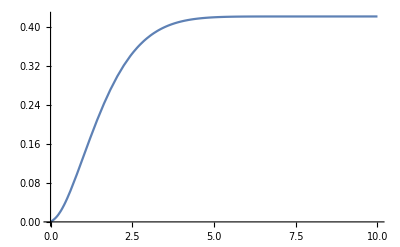

```mathematica
b=10;
Ω0=1;
τ=1;
Plot[NIntegrate[x Exp[-x]Coth[b x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,t}],{t,0,10}]
```

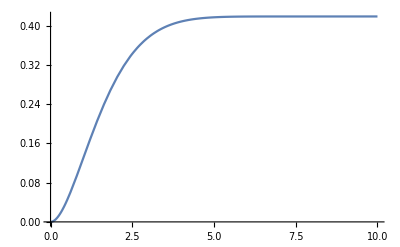

```mathematica
Ω0=1;
τ=1;
Plot[NIntegrate[x Exp[-x](1-Cos[(Ω0-x)τ])/(Ω0-x)^2,{x,0,t}],{t,0,10}]
```

```mathematica
2^0+2^1+2^3+2^4+2^5+2^6+2^7+2^9+2^10+2^11
```

3835

```mathematica
{{a11,a12},{a21,a22}}.{{b11,b12},{b21,b22}}
{{a11,a12},{a21,a22}}{{b11,b12},{b21,b22}}
```

{{a11 b11+a12 b21,a11 b12+a12 b22},{a21 b11+a22 b21,a21 b12+a22 b22}}

{{a11 b11,a12 b12},{a21 b21,a22 b22}}

```mathematica
Clear[L0,L1]
```

# Three qubit PMME

The LO is the error correction generator and L1 is the lindblad errors of 3 qubit

```mathematica
L0[η_]:=η{{0,1,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
L1[γ_]:=γ{{-3,1,0,0},{3,-3,2,0},{0,2,-3,3},{0,0,1,-3}};
Mat=L0[η]+ L1[γ];
Eigenvalues[Mat]
Eigensystem[Mat]
```

{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))}

{{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))},{{1,(3 γ)/(γ+η),(3 γ)/(γ+η),1},{1,-1,-1,1},{-1,-(-2 γ-η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),-(2 γ+η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),1},{-1,-(-2 γ-η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),-(2 γ+η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)),1}}}

Check that the Matrix is obtained by Q Lambda Inv(Q)

```mathematica
Λ=DiagonalMatrix[Eigensystem[Mat][[1]]];
Q=Transpose[Eigensystem[Mat][[2]]];
FullSimplify[Q.Λ.Inverse[Q]]//MatrixForm
Q//MatrixForm
```

(-3 γ | γ+η | 0 | 0
3 γ | -3 γ-η | 2 γ | 0
0 | 2 γ | -3 γ-η | 3 γ
0 | 0 | γ+η | -3 γ)

(1 | 1 | -1 | -1
(3 γ)/(γ+η) | -1 | -(-2 γ-η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η)) | -(-2 γ-η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η))
(3 γ)/(γ+η) | -1 | -(2 γ+η+√(16 γ^2+16 γ η+η^2))/(2 (γ+η)) | -(2 γ+η-√(16 γ^2+16 γ η+η^2))/(2 (γ+η))
1 | 1 | 1 | 1)

Since dv/dt = [L0] v + [L1 Q] Integrate[k (t')[Lambda[t] Inverse[Q]], {t', 0, t}]

```mathematica
FullSimplify[L1[γ].Q]//MatrixForm
```

(-(3 γ η)/(γ+η) | -4 γ | (γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | (γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(2 (γ+η))
(3 γ η)/(γ+η) | 4 γ | -(γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | -(γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η))
(3 γ η)/(γ+η) | 4 γ | (γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | (γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(2 (γ+η))
-(3 γ η)/(γ+η) | -4 γ | -(γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(2 (γ+η)) | (γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(2 (γ+η)))

```mathematica
Λ t//MatrixForm
MatrixExp[Λ t]//MatrixForm
```

(0 | 0 | 0 | 0
0 | t (-4 γ-η) | 0 | 0
0 | 0 | 1/2 t (-8 γ-η-√(16 γ^2+16 γ η+η^2)) | 0
0 | 0 | 0 | 1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2)))

(1 | 0 | 0 | 0
0 | ⅇ^(-t (4 γ+η)) | 0 | 0
0 | 0 | ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) | 0
0 | 0 | 0 | ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))))

Equation (154)

```mathematica
FullSimplify[MatrixExp[Λ t].Inverse[Q]]//MatrixForm
```

((γ+η)/(8 γ+2 η) | (γ+η)/(8 γ+2 η) | (γ+η)/(8 γ+2 η) | (γ+η)/(8 γ+2 η)
(3 ⅇ^(-t (4 γ+η)) γ)/(2 (4 γ+η)) | -(ⅇ^(-t (4 γ+η)) (γ+η))/(2 (4 γ+η)) | -(ⅇ^(-t (4 γ+η)) (γ+η))/(2 (4 γ+η)) | (3 ⅇ^(-t (4 γ+η)) γ)/(2 (4 γ+η))
(ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 γ+η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | -(ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))
-(ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (ⅇ^(1/2 t (-8 γ-η+√(16 γ^2+16 γ η+η^2))) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)))

Remember that thes ki  are the shifted kernel laplace transforms ki=k(s-lambda_i)

```mathematica
DΛ=DiagonalMatrix[{k0,k1,k2,k3}]
FullSimplify[DΛ.Inverse[Q]]//MatrixForm
```

{{k0,0,0,0},{0,k1,0,0},{0,0,k2,0},{0,0,0,k3}}

((k0 (γ+η))/(2 (4 γ+η)) | (k0 (γ+η))/(2 (4 γ+η)) | (k0 (γ+η))/(2 (4 γ+η)) | (k0 (γ+η))/(2 (4 γ+η))
(3 k1 γ)/(8 γ+2 η) | -(k1 (γ+η))/(2 (4 γ+η)) | -(k1 (γ+η))/(2 (4 γ+η)) | (3 k1 γ)/(8 γ+2 η)
(k2 (2 γ+η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (k2 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | -(k2 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (k2 (-2 γ-η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))
-(k3 (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(k3 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (k3 (γ+η))/(2 √(16 γ^2+16 γ η+η^2)) | (k3 (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)))

```mathematica
FullSimplify[L1[γ].Q].FullSimplify[DΛ.Inverse[Q]]//MatrixForm
```

(-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))
(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))
(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | (3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))
-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)) | -(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)))

```mathematica
PmmeMat3=-s IdentityMatrix[4]+L0[η]+FullSimplify[L1[γ].Q].FullSimplify[DΛ.Inverse[Q]]
```

{{-s-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),η-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (8 γ+7 η-√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))},{(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),-s-η+(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))},{(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-s-η+(3 k0 γ η)/(2 (4 γ+η))-(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),(3 k0 γ η)/(2 (4 γ+η))+(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))+(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))},{-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (2 γ+η-√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2)),-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)-(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))-(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),η-(3 k0 γ η)/(2 (4 γ+η))+(2 k1 γ (γ+η))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(4 √(16 γ^2+16 γ η+η^2)),-s-(3 k0 γ η)/(2 (4 γ+η))-(12 k1 γ^2)/(8 γ+2 η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)) (2 γ+η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))-(k2 γ (-2 γ-η+√(16 γ^2+16 γ η+η^2)) (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(8 (γ+η) √(16 γ^2+16 γ η+η^2))}}

```mathematica
FullSimplify[PmmeMat3]//MatrixForm
```

(-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

```mathematica
Clear[s,γ,η,k0,k1,k2,k3]
```

Let' s define the matrix as a function of parameter s, the error rate γ, the error correction rate η and the laplace transform of kernels ki.

```mathematica
Func3Qub[s_,γ_,η_,k0_,k1_,k2_,k3_]:=({{-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))), 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))), 1/4 (-4 s-4 η+(6 k0 γ η)/(4 γ+η)-(8 k1 γ (γ+η))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))}, {3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))), 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))), -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2))))}})
```

```mathematica
Simplify[Inverse[Func3Qub[s,γ,η,k0,k1,k2,k3]][[1,1]]]
```

-((4 s^3 (64 γ^3+80 γ^2 η+20 γ η^2+η^3)+24 γ^2 (4 k1 γ (γ+η)+η ((4-3 k0) γ+η)) (-k2 η √(16 γ^2+16 γ η+η^2)+k3 η √(16 γ^2+16 γ η+η^2)+k2 k3 (16 γ^2+16 γ η+η^2))+s^2 (832 k3 γ^4+512 γ^3 η-96 k0 γ^3 η+1040 k3 γ^3 η+640 γ^2 η^2-96 k0 γ^2 η^2+260 k3 γ^2 η^2+160 γ η^3-6 k0 γ η^3+13 k3 γ η^3+8 η^4-128 k3 γ^3 √(16 γ^2+16 γ η+η^2)-108 k3 γ^2 η √(16 γ^2+16 γ η+η^2)-19 k3 γ η^2 √(16 γ^2+16 γ η+η^2)+8 k1 γ (80 γ^3+112 γ^2 η+37 γ η^2+2 η^3)+k2 γ (4 γ+η) (208 γ^2+208 γ η+13 η^2+32 γ √(16 γ^2+16 γ η+η^2)+19 η √(16 γ^2+16 γ η+η^2)))+s (4 k1 γ (2 η (80 γ^3+112 γ^2 η+37 γ η^2+2 η^3)+k3 γ (448 γ^3+γ^2 (656 η-80 √(16 γ^2+16 γ η+η^2))+4 γ η (59 η-21 √(16 γ^2+16 γ η+η^2))+η^2 (13 η-19 √(16 γ^2+16 γ η+η^2)))+k2 γ (448 γ^3+16 γ^2 (41 η+5 √(16 γ^2+16 γ η+η^2))+η^2 (13 η+19 √(16 γ^2+16 γ η+η^2))+4 γ η (59 η+21 √(16 γ^2+16 γ η+η^2))))+η (-2 ((-8+3 k0) γ-2 η) η (16 γ^2+16 γ η+η^2)+k3 γ (-64 (-13+6 k0) γ^3+η^2 (13 η-19 √(16 γ^2+16 γ η+η^2))+4 γ η ((65-6 k0) η+3 (-7+2 k0) √(16 γ^2+16 γ η+η^2))+16 γ^2 ((65-24 k0) η+(-2+3 k0) √(16 γ^2+16 γ η+η^2))))+k2 γ (24 k3 γ (64 γ^3+80 γ^2 η+20 γ η^2+η^3)+η (-64 (-13+6 k0) γ^3+η^2 (13 η+19 √(16 γ^2+16 γ η+η^2))-4 γ η ((-65+6 k0) η+3 (-7+2 k0) √(16 γ^2+16 γ η+η^2))-16 γ^2 ((-65+24 k0) η+(-2+3 k0) √(16 γ^2+16 γ η+η^2))))))/(4 s (4 γ+η) (s+4 k1 γ+η) (s^2 (16 γ^2+16 γ η+η^2)+12 γ^2 (-k2 η √(16 γ^2+16 γ η+η^2)+k3 η √(16 γ^2+16 γ η+η^2)+k2 k3 (16 γ^2+16 γ η+η^2))+s (η (16 γ^2+16 γ η+η^2)+4 k3 γ (16 γ^2+16 γ η+η^2-2 γ √(16 γ^2+16 γ η+η^2)-η √(16 γ^2+16 γ η+η^2))+4 k2 γ (16 γ^2+η (η+√(16 γ^2+16 γ η+η^2))+2 γ (8 η+√(16 γ^2+16 γ η+η^2)))))))

Now let’s define the exponential kernel k(t)=c Exp[-ct] laplace transform

```mathematica
kLap[s_,c_]:=c/(s+c)
```

Now take the eigenvalues

```mathematica
Eigensystem[Mat][[1]]
```

{0,-4 γ-η,1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))}

```mathematica
Eigensystem[Mat][[1,2]]
```

-4 γ-η

```mathematica
Simplify[Inverse[Func3Qub[s,γ,η,kLap[s-Eigensystem[Mat][[1,1]],c],kLap[s-Eigensystem[Mat][[1,2]],c],kLap[s-Eigensystem[Mat][[1,3]],c],kLap[s-Eigensystem[Mat][[1,4]],c]]][[1,1]]]
```

-(1+(c (s^3+6 γ^2 (γ+η)+s^2 (9 γ+2 η)+s (20 γ^2+9 γ η+η^2)))/(s (s^3+12 γ^2 (4 γ+η)+2 s^2 (6 γ+η)+s (44 γ^2+12 γ η+η^2))))/(c+s)

```mathematica
FullSimplify[InverseLaplaceTransform[Inverse[Func3Qub[s,γ,η,kLap[s-Eigensystem[Mat][[1,1]],c],kLap[s-Eigensystem[Mat][[1,2]],c],kLap[s-Eigensystem[Mat][[1,3]],c],kLap[s-Eigensystem[Mat][[1,4]],c]]][[1,1]],s,t]]
```

1/4 (-(6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))-(2 (γ+η))/(4 γ+η)-(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c γ-16 γ^2+c η-13 γ η-η^2-c √(16 γ^2+16 γ η+η^2)-c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)+5 γ √(16 γ^2+16 γ η+η^2)+5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)+η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
q0t[t_,γ_,η_,c_]:=InverseLaplaceTransform[Inverse[-Func3Qub[s, γ, η, kLap[s - Eigensystem[Mat][[1, 1]], c], kLap[s - Eigensystem[Mat][[1, 2]], c], kLap[s - Eigensystem[Mat][[1, 3]], c], kLap[s - Eigensystem[Mat][[1, 4]], c]]][[1, 1]], s, t]
```

```mathematica
q1t[t_,γ_,η_,c_]:=InverseLaplaceTransform[Inverse[-Func3Qub[s, γ, η, kLap[s - Eigensystem[Mat][[1, 1]], c], kLap[s - Eigensystem[Mat][[1, 2]], c], kLap[s - Eigensystem[Mat][[1, 3]], c], kLap[s - Eigensystem[Mat][[1, 4]], c]]][[2, 1]], s, t]
```

```mathematica
FullSimplify[q0t[t,γ,η,c]]
```

1/4 ((6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))+(2 (γ+η))/(4 γ+η)+(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (-2 c γ+16 γ^2-c η+13 γ η+η^2+c √(16 γ^2+16 γ η+η^2)+c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)-5 γ √(16 γ^2+16 γ η+η^2)-5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)-η √(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
FullSimplify[q1t[t,γ,η,c]]
```

3/4 γ (2/(4 γ+η)-(2 c ⅇ^(-t (4 γ+η)))/((c-4 γ-η) (4 γ+η))-(4 ⅇ^(-c t) (c^2+6 γ^2-c (6 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c (-1+ⅇ^(t √(16 γ^2+16 γ η+η^2)))+8 γ+η-√(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (8 γ+η+√(16 γ^2+16 γ η+η^2))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))

```mathematica
q0tExplicit[t_,γ_,η_,c_]:=1/-4 (-(6 c ⅇ^(-t (4 γ+η)) γ)/((c-4 γ-η) (4 γ+η))-(2 (γ+η))/(4 γ+η)-(12 ⅇ^(-c t) γ (c^2+2 γ (7 γ+η)-c (8 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c γ-16 γ^2+c η-13 γ η-η^2-c √(16 γ^2+16 γ η+η^2)-c ⅇ^(t √(16 γ^2+16 γ η+η^2)) √(16 γ^2+16 γ η+η^2)+5 γ √(16 γ^2+16 γ η+η^2)+5 ⅇ^(t √(16 γ^2+16 γ η+η^2)) γ √(16 γ^2+16 γ η+η^2)+η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) η √(16 γ^2+16 γ η+η^2)+ⅇ^(t √(16 γ^2+16 γ η+η^2)) (16 γ^2+13 γ η+η^2-c (2 γ+η))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))
```

```mathematica
q1tExplicit[t_,γ_,η_,c_]:=3/4 γ (2/(4 γ+η)-(2 c ⅇ^(-t (4 γ+η)))/((c-4 γ-η) (4 γ+η))-(4 ⅇ^(-c t) (c^2+6 γ^2-c (6 γ+η)))/((-c+4 γ+η) (c^2+12 γ^2-c (8 γ+η)))+(c ⅇ^(-1/2 t (8 γ+η+√(16 γ^2+16 γ η+η^2))) (2 c (-1+ⅇ^(t √(16 γ^2+16 γ η+η^2)))+8 γ+η-√(16 γ^2+16 γ η+η^2)-ⅇ^(t √(16 γ^2+16 γ η+η^2)) (8 γ+η+√(16 γ^2+16 γ η+η^2))))/(√(16 γ^2+16 γ η+η^2) (c^2+12 γ^2-c (8 γ+η))))
```

```mathematica
qtExplicit[t_,γ_,η_,c_]:=q0tExplicit[t,γ,η,c]+q1tExplicit[t,γ,η,c]
```

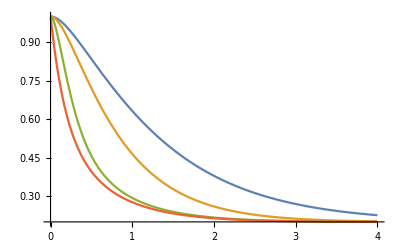

```mathematica
Plot[{q0tExplicit[t,1,1,1],q0tExplicit[t,1,1,2],q0tExplicit[t,1,1,10],q0tExplicit[t,1,1,1000]},{t,0,4}]
```

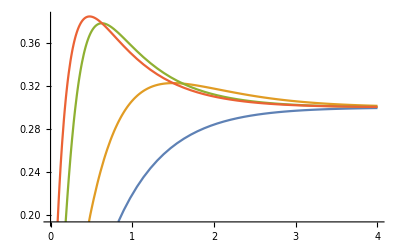

```mathematica
Plot[{q1tExplicit[t,1,1,1],q1tExplicit[t,1,1,2],q1tExplicit[t,1,1,10],q1tExplicit[t,1,1,1000]},{t,0,4}]
```

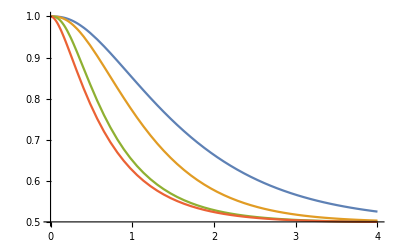

```mathematica
Plot[{qtExplicit[t,1,1,1],qtExplicit[t,1,1,2],qtExplicit[t,1,1,10],qtExplicit[t,1,1,1000]},{t,0,4}]
```

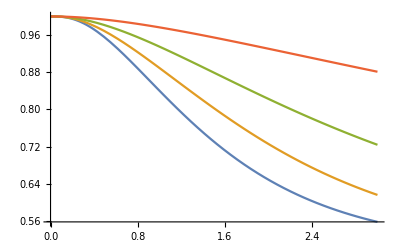

```mathematica
Plot[{qtExplicit[t,1,0,1],qtExplicit[t,1,6,1],qtExplicit[t,1,20,1],qtExplicit[t,1,80,1]},{t,0,3}]
```

now this is done in June 30

```mathematica
ResourceFunction["NInverseLaplaceTransform"][Exp[1-Sqrt[s]] s^(-3/4),s,3.7]
```

1.27511

```mathematica
Eigensystem[Mat][[1, 4]]
```

1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))

```mathematica
kLap[s_,c_]:=c/(s+c)
```

```mathematica
q0tNumerical[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-Func3Qub[s, γ, η, kLap[s , c], kLap[s - (-4 γ-η), c], kLap[s - 1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)), c], kLap[s - 1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2))]]][[1, 1]],s,t]
```

```mathematica
q0tNumerical[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-Func3Qub[s, γ, η,c/(s+c),c/((s- (-4 γ-η))+c), c/((s- 1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)))+c), c/((s - 1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2)))+c)]][[1, 1]],s,t]
```

```mathematica
q0tNumerical[0.1,1,1,1]
```

0.987611

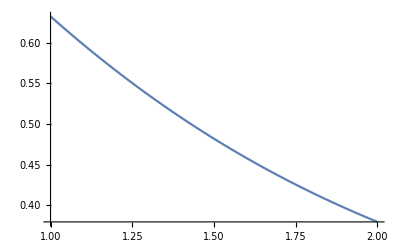

```mathematica
Plot[q0tNumerical[t,1,1,1],{t,1,2}]
```

```mathematica
Plot[{q0tExplicit[t,1,1,1]},{t,1,2}]
```

-Graphics-

```mathematica
kLapNum[s_,c_?NumericQ]:=c/(s+c)
kLapNum[s,c]
```

c/(c+s)

```mathematica
q0tNumer[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-Func3Qub[s, γ, η,kLapNum[s,c],kLapNum[s- (-4 γ-η),c],kLapNum[s- 1/2 (-8 γ-η-√(16 γ^2+16 γ η+η^2)),c], kLapNum[s- 1/2 (-8 γ-η+√(16 γ^2+16 γ η+η^2)),c]]][[1, 1]],s,t]
```

```mathematica
q0tExplicit[2,1,1,1]
```

1/4 (4/5-3/(10 ⅇ^10)+6/ⅇ^2-(ⅇ^(-9-√33) (-27+5 √33+27 ⅇ^(2 √33)+5 √33 ⅇ^(2 √33)))/(4 √33))

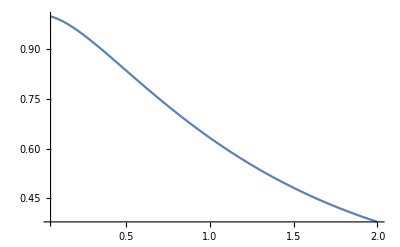

```mathematica
Plot[q0tNumer[t,1,1,1],{t,0.05,2}]
```

## Finally try to combine all

```mathematica
kLapExpKernel[s_,c_,λ_]:=c/((s-λ)+c)
```

```mathematica
L0[η_]:=η{{0,1,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}};
L1[γ_]:=γ{{-3,1,0,0},{3,-3,2,0},{0,2,-3,3},{0,0,1,-3}};
(*==L0[η]+L1[γ]*)FullSimplify[Transpose[Eigenvectors[L0[η]+L1[γ]]].DiagonalMatrix[Eigenvalues[L0[η]+L1[γ]]].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]]];
(*L1[γ].Q]==*)
FullSimplify[L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]];
(*DΛ.Inverse[Q]*)
DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]];
FullSimplify[(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])]//MatrixForm
PmmeMat3[s_,γ_,η_,k0_,k1_,k2_,k3_]:=-s IdentityMatrix[4]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{k0,k1,k2,k3}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
FullSimplify[PmmeMat3[s,γ,η,k0,k1,k2,k3]]//MatrixForm
```

(3/4 γ (-(2 (4 k1 γ+k0 η))/(4 γ+η)+k3 (-1-η/(√(16 γ^2+16 γ η+η^2)))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)+k3 (4 γ+η))/(4 γ+η)+(-k3 (8 γ+7 η)+k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)-5 k3 (4 γ+η))/(4 γ+η)+(k3 (16 γ+11 η)-k2 (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)-5 k3 (4 γ+η))/(4 γ+η)+(k3 (16 γ+11 η)-k2 (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)+k3 (4 γ+η))/(4 γ+η)+(-k3 (8 γ+7 η)+k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-(2 (4 k1 γ+k0 η))/(4 γ+η)+k3 (-1-η/(√(16 γ^2+16 γ η+η^2)))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

(-s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-(2 (4 k1 γ (γ+η)+2 s (4 γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (-k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (8 γ-η)+k2 (-8 γ+η-√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((6 k0 η-8 k1 (γ+η)+5 k3 (4 γ+η))/(4 γ+η)+(16 (k2-k3) γ+11 (k2-k3) η+5 k2 √(16 γ^2+16 γ η+η^2))/(√(16 γ^2+16 γ η+η^2))) | 1/4 (-(2 (4 k1 γ (γ+η)+2 s (4 γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (16 γ+11 η-5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))-(k2 γ (16 γ+11 η+5 √(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 3/4 γ (k3+(8 k1 γ+2 k0 η)/(4 γ+η)+(k3 (-8 γ+η)+k2 (8 γ-η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2)))
3/4 γ (k2+k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k2 η)/(√(16 γ^2+16 γ η+η^2))+(k3 η)/(√(16 γ^2+16 γ η+η^2))) | 1/4 γ ((-6 k0 η+8 k1 (γ+η)-k3 (4 γ+η))/(4 γ+η)+(k3 (8 γ+7 η)-k2 (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | 1/4 ((2 (4 k1 γ (γ+η)+η (8 γ-3 k0 γ+2 η)))/(4 γ+η)+(k3 γ (-8 γ-7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))+(k2 γ (8 γ+7 η+√(16 γ^2+16 γ η+η^2)))/(√(16 γ^2+16 γ η+η^2))) | -s+3/4 γ (-k3-(2 (4 k1 γ+k0 η))/(4 γ+η)-(k3 η)/(√(16 γ^2+16 γ η+η^2))+k2 (-1+η/(√(16 γ^2+16 γ η+η^2)))))

```mathematica
PmmeMat3ExpKernel[s_,γ_,η_,c_]:=-s IdentityMatrix[4]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[4]]]}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
q0tNum[t_,γ_,η_,c_]:=ResourceFunction["NInverseLaplaceTransform"][Inverse[-FullSimplify[PmmeMat3ExpKernel[s,γ,η,c]]][[1, 1]],s,t]
```

```mathematica
Plot[q0tNum[t,1,1,1],{t,0.05,2}]
```

-Graphics-

## Five qubit code

```mathematica
L0five[η_]:=η{{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,1,-1/3,1,2/3,1/2,1/3,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1/3,0,-5/6,1/2,1/3,0,0,1/2,1/9,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,1/3,0,1/6,0,1/3,0,0,1/2,-1/9,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0}}

L1five[γ_]:=γ{{-15,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{15,-13,2,2,0,0,0,0,0,0,0,0,0,0,0,0},{0,4,-15,2,3,1,0,0,0,0,0,0,0,0,0,0},{0,8,4,-13,0,2,3,0,0,0,0,0,0,0,0,0},{0,0,3,0,-15,1,0,0,1,0,4,0,0,0,0,0},{0,0,6,6,6,-12,6,4,3,2,0,0,0,0,0,0},{0,0,0,3,0,2,-15,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,0,-15,3,4,0,0,3,1,0,0},{0,0,0,0,4,2,0,4,-14,0,8,4,2,0,2,0},{0,0,0,0,0,2,6,4,3,-11,0,0,0,4,3,0},{0,0,0,0,2,0,0,0,1,0,-15,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,2,-14,2,0,2,10},{0,0,0,0,0,0,0,2,1,0,0,4,-12,2,2,0},{0,0,0,0,0,0,0,1,0,2,0,0,3,-11,6,0},{0,0,0,0,0,0,0,0,1,1,0,4,2,4,-15,5},{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,-15}};
MatrixForm[L0five[1]]
MatrixForm[L1five[1]]
```

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | -1/3 | 1 | 2/3 | 1/2 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | -5/6 | 1/2 | 1/3 | 0 | 0 | 1/2 | 1/9 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | 1/2 | -1/9 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

(-15 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | -13 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | -15 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 4 | -13 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | -15 | 1 | 0 | 0 | 1 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 6 | 6 | -12 | 6 | 4 | 3 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | -15 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | -15 | 3 | 4 | 0 | 0 | 3 | 1 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 4 | -14 | 0 | 8 | 4 | 2 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 2 | 6 | 4 | 3 | -11 | 0 | 0 | 0 | 4 | 3 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -15 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | -14 | 2 | 0 | 2 | 10
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 4 | -12 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 3 | -11 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 4 | 2 | 4 | -15 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | -15)

```mathematica
MatrixForm[Transpose[N[Eigenvectors[L0five[1]+L1five[1]]]].DiagonalMatrix[N[Eigenvalues[L0five[1]+L1five[1]]]].Inverse[Transpose[N[Eigenvectors[L0five[1]+L1five[1]]]]]]
```

(-15.+1.5024×10^-31 ⅈ | -8.58681×10^-16+4.55842×10^-32 ⅈ | -7.12405×10^-16+4.71301×10^-32 ⅈ | -6.569×10^-16+7.5098×10^-32 ⅈ | -3.9399×10^-16+5.80918×10^-32 ⅈ | -3.01375×10^-16+8.976×10^-32 ⅈ | -2.6232×10^-16+7.49069×10^-32 ⅈ | 4.70793×10^-17+1.01487×10^-31 ⅈ | 2.60524×10^-17+8.27862×10^-32 ⅈ | 1.13511×10^-16+1.02521×10^-31 ⅈ | -2.21896×10^-17+5.60627×10^-32 ⅈ | 2.41249×10^-16+6.08556×10^-32 ⅈ | 2.53695×10^-16+8.40603×10^-32 ⅈ | 3.38241×10^-16+8.097×10^-32 ⅈ | 3.16708×10^-16+6.95838×10^-32 ⅈ | 3.0036×10^-16+1.21191×10^-32 ⅈ
15.+7.96257×10^-15 ⅈ | -14.-2.87277×10^-16 ⅈ | 2.+5.00943×10^-16 ⅈ | 2.+5.14491×10^-17 ⅈ | -6.02551×10^-15-2.16628×10^-16 ⅈ | -3.09566×10^-15+1.8443×10^-16 ⅈ | -7.22101×10^-16-2.17224×10^-16 ⅈ | 3.81575×10^-15+6.65667×10^-16 ⅈ | 2.56743×10^-15+3.50365×10^-16 ⅈ | 6.16996×10^-15+3.15128×10^-16 ⅈ | -2.89665×10^-15+1.36595×10^-16 ⅈ | 2.37335×10^-15+2.09857×10^-16 ⅈ | 5.44908×10^-15+3.83649×10^-16 ⅈ | 9.20041×10^-15+5.51584×10^-17 ⅈ | 8.17237×10^-15-1.63146×10^-16 ⅈ | 7.27715×10^-16+2.36814×10^-16 ⅈ
-1.91288×10^-13+7.95157×10^-14 ⅈ | 4.-1.79482×10^-15 ⅈ | -16.+1.72552×10^-15 ⅈ | 2.+2.51161×10^-16 ⅈ | 3.-2.10193×10^-15 ⅈ | 1.+1.6501×10^-15 ⅈ | 9.55618×10^-16-3.17522×10^-15 ⅈ | -2.30167×10^-16+7.49699×10^-15 ⅈ | -1.50352×10^-15+4.00744×10^-15 ⅈ | 3.43504×10^-15+3.64395×10^-15 ⅈ | 8.76324×10^-16+2.01064×10^-15 ⅈ | 2.16174×10^-15+2.1533×10^-15 ⅈ | 1.35031×10^-15+4.41183×10^-15 ⅈ | 6.79698×10^-16+2.06689×10^-16 ⅈ | -2.77797×10^-15-2.00128×10^-15 ⅈ | 4.1629×10^-15-3.36085×10^-17 ⅈ
1.67435×10^-13-1.05041×10^-13 ⅈ | 8.+3.09373×10^-15 ⅈ | 4.-5.03223×10^-15 ⅈ | -14.-5.32061×10^-16 ⅈ | 3.09967×10^-15+2.91882×10^-15 ⅈ | 2.-1.8944×10^-15 ⅈ | 3.+3.30124×10^-15 ⅈ | 1.23231×10^-15-9.72805×10^-15 ⅈ | 1.28052×10^-15-5.09155×10^-15 ⅈ | -3.22649×10^-15-4.67915×10^-15 ⅈ | 1.80563×10^-15-2.41815×10^-15 ⅈ | 1.91473×10^-16-2.76677×10^-15 ⅈ | -9.11428×10^-16-5.67709×10^-15 ⅈ | -2.0852×10^-15-3.78743×10^-16 ⅈ | 8.16651×10^-16+2.42944×10^-15 ⅈ | -1.74939×10^-15-1.74855×10^-15 ⅈ
1.48841×10^-13-1.21601×10^-13 ⅈ | 4.37692×10^-15+3.28966×10^-15 ⅈ | 3.-5.23573×10^-15 ⅈ | -1.37158×10^-15-6.59916×10^-16 ⅈ | -16.+3.55481×10^-15 ⅈ | 1.-2.44666×10^-15 ⅈ | -7.27342×10^-15+4.31378×10^-15 ⅈ | 5.99528×10^-15-1.12696×10^-14 ⅈ | 1.-5.91186×10^-15 ⅈ | 1.42399×10^-15-5.42817×10^-15 ⅈ | 4.-2.85944×10^-15 ⅈ | 9.38585×10^-17-2.50086×10^-15 ⅈ | 3.9552×10^-15-6.61069×10^-15 ⅈ | 1.96029×10^-15-4.77409×10^-16 ⅈ | 1.98206×10^-15+2.84961×10^-15 ⅈ | -4.55447×10^-15-7.50532×10^-16 ⅈ
-1.75753×10^-13+1.72851×10^-13 ⅈ | 4.08507×10^-14-5.73134×10^-15 ⅈ | 7.+8.34592×10^-15 ⅈ | 7.+1.41216×10^-15 ⅈ | 7.-4.16394×10^-15 ⅈ | -12.3333+3.66762×10^-15 ⅈ | 7.-5.04604×10^-15 ⅈ | 4.66667+1.47041×10^-14 ⅈ | 3.5+8.15579×10^-15 ⅈ | 2.33333+7.37057×10^-15 ⅈ | 8.42118×10^-15+3.72898×10^-15 ⅈ | -1.15486×10^-14+4.31805×10^-15 ⅈ | -2.58756×10^-14+8.7259×10^-15 ⅈ | -3.01703×10^-14+9.96452×10^-16 ⅈ | -2.71016×10^-14-3.78792×10^-15 ⅈ | -5.24797×10^-15+4.51475×10^-15 ⅈ
1.62207×10^-13-4.44146×10^-15 ⅈ | 3.10361×10^-14+8.8236×10^-16 ⅈ | 2.03886×10^-14-1.12458×10^-15 ⅈ | 3.-1.92751×10^-16 ⅈ | 9.97252×10^-15-8.5963×10^-16 ⅈ | 2.-3.1706×10^-16 ⅈ | -16.-9.51605×10^-16 ⅈ | -6.32821×10^-15+4.55202×10^-16 ⅈ | -4.15298×10^-15+4.20238×10^-16 ⅈ | 2.-8.42709×10^-17 ⅈ | 2.27294×10^-16+2.05146×10^-16 ⅈ | -2.05371×10^-15-2.01215×10^-16 ⅈ | -2.91188×10^-15+1.88188×10^-16 ⅈ | -1.13384×10^-14-2.96883×10^-16 ⅈ | -5.85316×10^-15-2.7494×10^-16 ⅈ | -2.6678×10^-15-2.17305×10^-15 ⅈ
-2.0694×10^-14-5.84856×10^-14 ⅈ | -3.87321×10^-14+8.23687×10^-16 ⅈ | -3.22348×10^-14-6.11782×10^-16 ⅈ | -2.36177×10^-14-1.92393×10^-16 ⅈ | -1.7836×10^-14+3.60851×10^-15 ⅈ | 2.33333-9.34669×10^-16 ⅈ | -1.39434×10^-14+2.98956×10^-15 ⅈ | -15.8333-6.81574×10^-15 ⅈ | 3.5-3.96863×10^-15 ⅈ | 4.33333-2.96808×10^-15 ⅈ | -4.24473×10^-15-2.542×10^-15 ⅈ | -1.40299×10^-16-1.18306×10^-15 ⅈ | 3.5-3.52112×10^-15 ⅈ | 1.11111+6.46468×10^-18 ⅈ | 1.01642×10^-14+2.03141×10^-15 ⅈ | -3.81631×10^-15+1.80407×10^-15 ⅈ
-1.92697×10^-13-2.81905×10^-14 ⅈ | -2.69573×10^-15+3.53433×10^-15 ⅈ | -1.3837×10^-15-4.10324×10^-15 ⅈ | -4.35318×10^-15-7.65399×10^-16 ⅈ | 4.-2.61646×10^-15 ⅈ | 2.-1.12637×10^-15 ⅈ | 2.48446×10^-15-1.54188×10^-15 ⅈ | 4.+1.46738×10^-16 ⅈ | -15.+7.86803×10^-16 ⅈ | 5.19208×10^-15-7.48011×10^-16 ⅈ | 8.-1.40052×10^-17 ⅈ | 4.-1.01925×10^-15 ⅈ | 2.-3.375×10^-16 ⅈ | 5.09139×10^-15-7.51341×10^-16 ⅈ | 2.-4.35369×10^-16 ⅈ | -3.86563×10^-15-6.85306×10^-15 ⅈ
-5.05473×10^-14-3.45018×10^-15 ⅈ | -5.42404×10^-14-6.10436×10^-16 ⅈ | -3.76392×10^-14+2.16331×10^-16 ⅈ | -3.06786×10^-14+3.01829×10^-16 ⅈ | -1.96631×10^-14+1.22186×10^-15 ⅈ | 2.+4.12408×10^-16 ⅈ | 6.+4.73173×10^-16 ⅈ | 4.-1.05178×10^-15 ⅈ | 3.-1.01101×10^-15 ⅈ | -12.-4.01059×10^-17 ⅈ | -7.7347×10^-15+4.00719×10^-16 ⅈ | 5.49192×10^-15+5.32606×10^-16 ⅈ | 1.16934×10^-14-5.07084×10^-16 ⅈ | 4.+2.80163×10^-16 ⅈ | 3.+2.79114×10^-16 ⅈ | 2.31853×10^-15+1.61361×10^-15 ⅈ
6.9608×10^-14+4.77612×10^-14 ⅈ | -4.70741×10^-15-1.53342×10^-15 ⅈ | 5.50838×10^-16+1.90475×10^-15 ⅈ | 2.14897×10^-15+4.89915×10^-16 ⅈ | 2.-8.53015×10^-16 ⅈ | 2.41609×10^-15+1.03756×10^-15 ⅈ | 6.69652×10^-15-1.34535×10^-15 ⅈ | 1.02182×10^-15+4.07098×10^-15 ⅈ | 1.+2.01074×10^-15 ⅈ | 3.85491×10^-15+2.0553×10^-15 ⅈ | -16.+1.72771×10^-15 ⅈ | 1.+1.34611×10^-15 ⅈ | 2.84273×10^-15+2.47472×10^-15 ⅈ | 6.66127×10^-15+2.94968×10^-16 ⅈ | 8.16783×10^-15-9.5176×10^-16 ⅈ | 1.31798×10^-14+9.26793×10^-16 ⅈ
-1.36845×10^-13+3.83256×10^-14 ⅈ | 5.82209×10^-16-2.20955×10^-15 ⅈ | -3.96753×10^-17+2.5929×10^-15 ⅈ | -2.12554×10^-15+5.4353×10^-16 ⅈ | 3.07372×10^-16-1.34224×10^-16 ⅈ | -2.86709×10^-15+8.8451×10^-16 ⅈ | -6.20158×10^-15-3.05001×10^-16 ⅈ | -4.76694×10^-15+2.97644×10^-15 ⅈ | 1.+1.57934×10^-15 ⅈ | -5.33237×10^-15+1.67241×10^-15 ⅈ | 2.+4.18165×10^-17 ⅈ | -15.+1.11327×10^-15 ⅈ | 2.+2.04625×10^-15 ⅈ | -6.68676×10^-15+2.77806×10^-16 ⅈ | 2.-4.16714×10^-16 ⅈ | 10.+3.17999×10^-15 ⅈ
1.71207×10^-13-3.44944×10^-15 ⅈ | 2.77951×10^-14+4.9933×10^-16 ⅈ | 2.07833×10^-14-6.52729×10^-16 ⅈ | 1.91302×10^-14-1.89483×10^-16 ⅈ | 9.62503×10^-15-9.32658×10^-16 ⅈ | 5.5813×10^-15-1.5675×10^-16 ⅈ | 9.05532×10^-15-3.74566×10^-16 ⅈ | 2.+2.54849×10^-16 ⅈ | 1.+1.378×10^-16 ⅈ | -6.21459×10^-15-8.77907×10^-17 ⅈ | 2.02528×10^-15+4.97396×10^-16 ⅈ | 4.-1.00689×10^-17 ⅈ | -13.-1.26117×10^-16 ⅈ | 2.-5.91962×10^-17 ⅈ | 2.-2.50642×10^-16 ⅈ | 1.98137×10^-15-1.06911×10^-15 ⅈ
8.06241×10^-15+2.6224×10^-15 ⅈ | 6.93612×10^-15+8.17701×10^-16 ⅈ | 8.78196×10^-15-9.96109×10^-16 ⅈ | 3.83082×10^-15-1.61682×10^-16 ⅈ | 9.41922×10^-15-1.30021×10^-15 ⅈ | 0.333333-3.45559×10^-16 ⅈ | 2.94262×10^-15-8.82987×10^-16 ⅈ | 1.16667+1.19069×10^-15 ⅈ | -1.29656×10^-15+1.09721×10^-15 ⅈ | 2.33333+2.52499×10^-16 ⅈ | -4.83294×10^-16-1.65866×10^-16 ⅈ | 7.13346×10^-16-4.02361×10^-16 ⅈ | 3.5+5.08203×10^-16 ⅈ | -11.1111-3.23148×10^-16 ⅈ | 7.-2.56006×10^-16 ⅈ | -6.96216×10^-15-1.81917×10^-15 ⅈ
-3.00101×10^-14+3.31784×10^-15 ⅈ | 3.88699×10^-15-9.65907×10^-16 ⅈ | -1.80318×10^-15+1.16762×10^-15 ⅈ | 3.28647×10^-15+2.08926×10^-16 ⅈ | -3.66188×10^-15+2.22081×10^-15 ⅈ | -1.54896×10^-15+4.73408×10^-16 ⅈ | -5.51294×10^-15+8.2217×10^-16 ⅈ | -2.49655×10^-16-1.19563×10^-15 ⅈ | 1.-9.24337×10^-16 ⅈ | 1.-7.08875×10^-17 ⅈ | 6.6157×10^-15+1.71672×10^-16 ⅈ | 4.+5.97635×10^-16 ⅈ | 2.-2.74093×10^-16 ⅈ | 4.+3.81462×10^-16 ⅈ | -16.+4.76649×10^-16 ⅈ | 5.+1.92268×10^-15 ⅈ
5.07795×10^-15-2.97469×10^-14 ⅈ | -3.58794×10^-15+1.18652×10^-15 ⅈ | -1.27544×10^-15-1.6482×10^-15 ⅈ | -2.35032×10^-15-3.17439×10^-16 ⅈ | -8.04146×10^-17-1.93038×10^-16 ⅈ | -2.47304×10^-16-6.78457×10^-16 ⅈ | 2.65547×10^-16+4.34081×10^-16 ⅈ | 2.80859×10^-15-2.27734×10^-15 ⅈ | 1.82176×10^-15-1.04007×10^-15 ⅈ | 3.2025×10^-15-1.32494×10^-15 ⅈ | 2.-5.69813×10^-16 ⅈ | 2.-9.88333×10^-16 ⅈ | 3.22618×10^-15-1.64914×10^-15 ⅈ | 2.73831×10^-15-1.74938×10^-16 ⅈ | 2.55021×10^-15+4.26458×10^-16 ⅈ | -15.-1.37544×10^-15 ⅈ)

```mathematica
PmmeMat5ExpKernelExact[s_,γ_,η_,c_]:=-s IdentityMatrix[16]+L0[η]+(L1[γ].Transpose[Eigenvectors[L0[η]+L1[γ]]]).(DiagonalMatrix[{kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[1]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[2]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[3]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[4]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[5]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[6]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[7]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[8]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[9]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[10]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[11]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[12]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[13]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[14]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[15]]],kLapExpKernel[s,c,Eigenvalues[L0[η]+L1[γ]][[16]]]]}].Inverse[Transpose[Eigenvectors[L0[η]+L1[γ]]]])
```

```mathematica
(**)
PmmeMat5ExpKernel[s_,γ_,η_,c_]:=-s IdentityMatrix[16]+L0five[η]+(L1five[γ].Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]).(DiagonalMatrix[{kLapExpKernel[s,c,N[Eigenvalues[L0[η]+L1[γ]]][[1]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[2]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[3]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[4]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[5]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[6]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[7]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[8]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[9]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[10]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[11]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[12]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[13]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[14]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[15]]],kLapExpKernel[s,c,N[Eigenvalues[L0five[η]+L1five[γ]]][[16]]]}].Inverse[Transpose[N[Eigenvectors[L0five[η]+L1five[γ]]]]])
```

```mathematica
FuPmmeMat5ExpKernel[s,1,1,1]
```

## THIS IS OTHER

```mathematica
M={{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-κ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-κ/2,0,0,0,0,-2α,0,0,0,0,0,0,0,0},{-κ,0,0,-κ,0,0,2α,0,0,0,0,0,0,0,0,0},{0,0,0,0,-η,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2α,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0},{0,0,2α,0,-κ,0,0,-η-κ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-η,0,0,0,0,-2α,0,0},{0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,-2α,0,0,0},{0,0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,-κ,0,0,-η-κ,0,0,0,0},{η,0,0,0,0,0,0,0,0,2α,0,0,-η,0,0,0},{0,η,0,0,0,0,0,0,2α,0,0,0,0,-η-κ/2,0,0},{0,0,η,0,0,0,0,0,0,0,0,0,0,0,-η-κ/2,0},{0,0,0,η,0,0,0,0,0,0,0,0,-κ,0,0,-η-κ}}
MatrixForm[M]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-κ/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-κ/2,0,0,0,0,-2 α,0,0,0,0,0,0,0,0},{-κ,0,0,-κ,0,0,2 α,0,0,0,0,0,0,0,0,0},{0,0,0,0,-η,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0,0},{0,0,0,-2 α,0,0,-η-κ/2,0,0,0,0,0,0,0,0,0},{0,0,2 α,0,-κ,0,0,-η-κ,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-η,0,0,0,0,-2 α,0,0},{0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,-2 α,0,0,0},{0,0,0,0,0,0,0,0,0,0,-η-κ/2,0,0,0,0,0},{0,0,0,0,0,0,0,0,-κ,0,0,-η-κ,0,0,0,0},{η,0,0,0,0,0,0,0,0,2 α,0,0,-η,0,0,0},{0,η,0,0,0,0,0,0,2 α,0,0,0,0,-η-κ/2,0,0},{0,0,η,0,0,0,0,0,0,0,0,0,0,0,-η-κ/2,0},{0,0,0,η,0,0,0,0,0,0,0,0,-κ,0,0,-η-κ}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -κ/2 | 0 | 0 | 0 | 0 | -2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-κ | 0 | 0 | -κ | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 α | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 α | 0 | -κ | 0 | 0 | -η-κ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η | 0 | 0 | 0 | 0 | -2 α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | -2 α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ | 0 | 0 | -η-κ | 0 | 0 | 0 | 0
η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | -η | 0 | 0 | 0
0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 2 α | 0 | 0 | 0 | 0 | -η-κ/2 | 0 | 0
0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -η-κ/2 | 0
0 | 0 | 0 | η | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -κ | 0 | 0 | -η-κ)

```mathematica
FullSimplify[NullSpace[M]]
```

{{((η+κ) (-1-(8 α^2)/(η (2 η+κ))) (8 α^2+κ (2 η+κ)))/(κ (16 α^2+(η+κ) (2 η+κ))),0,0,((η+κ) (8 α^2+η (2 η+κ)))/(η (16 α^2+(η+κ) (2 η+κ))),0,0,-(4 α (η+κ) (8 α^2+η (2 η+κ)))/(η (2 η+κ) (16 α^2+(η+κ) (2 η+κ))),0,0,(4 α (η+κ) (8 α^2+κ (2 η+κ)))/(κ (2 η+κ) (16 α^2+(η+κ) (2 η+κ))),0,0,-((η+κ) (8 α^2+κ (2 η+κ)))/(κ (16 α^2+(η+κ) (2 η+κ))),0,0,1}}